# Testing one particular ttH@NNLO supergraph

```mathematica
Quit[]
```

## Resources

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
<<"../../ltd_math_utils/LTDTools.m"
```

The documented functions in this package are: 
 ?plotGraph 
 ?findIsomorphicGraphs 
 ?constructCuts 
 ?importGraphs 
 ?getLoopLines 
 ?getCutStructure 
 ?writeMinimalJSON 
 ?extractTensCoeff 
 ?getSymCoeff 
 ?processNumerator 
 ?createSuperGraph 
 ?translateToFeynCalc 
 ?getSymCoeffSP
 ----------------------------------------- 
 Needs the package FeynCalc which can installed with Import["https://raw.githubusercontent.com/FeynCalc/feyncalc/master/install.m"]; InstallFeynCalc[]
 Needs the package IGraphM which can be downloaded from https://github.com/szhorvat/IGraphM. !!! 
 Run: Get["https://raw.githubusercontent.com/szhorvat/IGraphM/master/IGInstaller.m"] for installation.

FeynCalc 9.3.0 (stable version). For help, use the documentation center, check out the wiki or write to the mailing list.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, P3H-20-002, TTP19-020, TUM-EFT 130/19, arXiv:2001.04407

• V. Shtabovenko, R. Mertig and F. Orellana, Comput. Phys. Commun., 207, 432-444, 2016, arXiv:1601.01167

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun., 64, 345-359, 1991.

```mathematica
MyPrint[msg_]:=Print[Style[msg,FontFamily->"Monaco"]];
```

## Extracting the one ttH diagram of interest

```mathematica
(* First load all ttH  graphs *)
allTTHGraphs=importGraphs["./epem_ttH.qgr",sumIsoGraphs->False];
```

So we have many of them

```mathematica
Length[allTTHGraphs]
```

744

Many are however now the desired one, for instance:

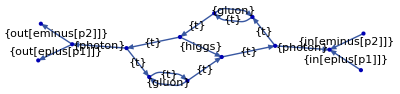

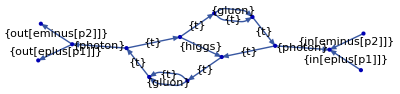

```mathematica
{plotGraph[allTTHGraphs⟦1⟧,edgeLabels->{"particleType"}],
plotGraph[allTTHGraphs⟦4⟧,edgeLabels->{"particleType"}]};
```

We can check if two diagrams are isomorphic simply with

```mathematica
findIsomorphicGraphs[allTTHGraphs⟦1;;4⟧,edgeTagging->{"particleType"}]
```

({3,2} | {}
{4,1} | {<|vertexMap→<|in(1)→in(1),v(1)→v(1),in(2)→in(2),out(1)→out(1),v(2)→v(2),out(2)→out(2),v(3)→v(3),v(4)→v(4),v(5)→v(5),v(6)→v(6),v(7)→v(7),v(8)→v(8),v(9)→v(9),v(10)→v(10)|>,permutation→Cycles[{}],orientationChange→{1,1,1,1,1,1,-1,-1,-1,-1,1,-1,1,-1,-1,1,-1}|>})

And we are only interested in one particular diagram which we will build here in order to find it in the list:

```mathematica
TargetDiagram=<|
"edges"->{
(* incoming photon *)
in[1]->v[1],in[2]->v[1],v[1]->v[3],
(* outgoing photon *)
v[4]->v[2],v[2]->out[1],v[2]->out[2],
(* top quark loop upper branch *)
v[3]->v[5],v[5]->v[6],v[6]->v[4],
(* top quark loop lower branch *)
v[4]->v[7],v[7]->v[8],v[8]->v[9],v[9]->v[10],v[10]->v[3],
(* gluons *)
v[5]->v[9],v[6]->v[8],
(* Higgs *)
v[10]->v[7]
},
"particleType"->{
in[eplus[p1]],in[eminus[p2]],photon,
photon,out[eplus[p1]],out[eminus[p2]],
t,t,t,
t,t,t,t,t,
gluon,gluon,
higgs
}
|>;
```

Now let’s find it in the list of diagrams

```mathematica
FindMyDiagram[diag_,OptionsPattern[{DEBUG->False}]]:=Block[
{diagIDsFound={}},
For[i=1,i≤Length[allTTHGraphs],++i,
If[OptionValue[DEBUG],Print["Now comparing with diag ID="<>ToString[i]];];
If[
findIsomorphicGraphs[{allTTHGraphs⟦i⟧,diag},edgeTagging->{"particleType"}]≠{},
AppendTo[diagIDsFound,i];
];
];
diagIDsFound
]
```

```mathematica
FindMyDiagram[TargetDiagram]
```

{65,72}

Check if these two diagrams are indeed the desired ones!

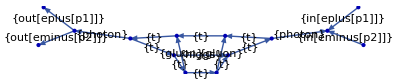

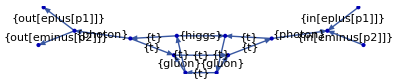

```mathematica
{plotGraph[allTTHGraphs⟦65⟧,edgeLabels->{"particleType"}],
plotGraph[allTTHGraphs⟦72⟧,edgeLabels->{"particleType"}]};
```

Yes they are!

```mathematica
SelectedDiagram=allTTHGraphs⟦65⟧;
```

## Processing that diagram

### Cutkosky cuts

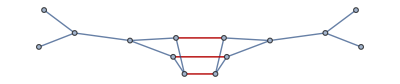

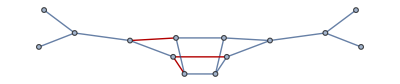

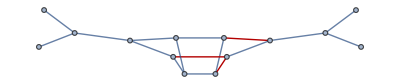

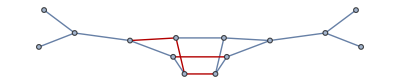

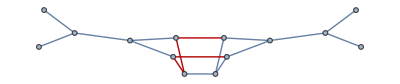

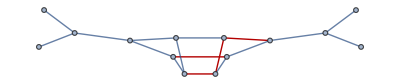

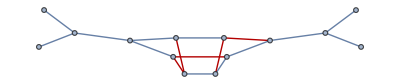

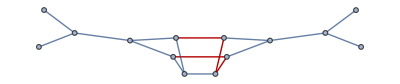

```mathematica
AllCutkoskyCutsOfSelectedDiagram=constructCuts[SelectedDiagram];
```

Below is a hard-coded filter to select only the 9 cutkosky cuts I am interested in

```mathematica
FilterCutkoskyCuts[allCuts_]:=Block[
{nTopCuts,nHiggsCuts,i,selectedCuts={},iCut,cutIndices},
For[i=1,i≤Length[allCuts],i++,
nTopCuts=0;
nHiggsCuts=0;
For[iCut=1,iCut≤Length[allCuts⟦i⟧["cutInfo"]],iCut++,
If[And[allCuts⟦i⟧["cutInfo"]⟦iCut⟧=="cut",allCuts⟦i⟧["particleType"]⟦iCut⟧==t],nTopCuts+=1;];
If[And[allCuts⟦i⟧["cutInfo"]⟦iCut⟧=="cut",allCuts⟦i⟧["particleType"]⟦iCut⟧==higgs],nHiggsCuts+=1;];
];
If[And[nTopCuts==2,nHiggsCuts==1],
AppendTo[selectedCuts,allCuts⟦i⟧];
];
];
selectedCuts
]
```

```mathematica
AllSelectedCutkoskyCutsOfSelectedDiagram=FilterCutkoskyCuts[AllCutkoskyCutsOfSelectedDiagram];
```

We should be left with 9 cuts.

```mathematica
Length[AllSelectedCutkoskyCutsOfSelectedDiagram]
```

9

Which are these:

```mathematica
Block[{graph,edges,i},
For[i=1,i≤Length[AllSelectedCutkoskyCutsOfSelectedDiagram],i++,
graph=AllSelectedCutkoskyCutsOfSelectedDiagram⟦i⟧;
edges=graph⟦"edges"⟧/. Rule[a_,b_]:>UndirectedEdge[a,b] /. DirectedEdge[a_,b_]:>UndirectedEdge[a,b]/. TwoWayRule[a_,b_]:>UndirectedEdge[a,b];
Print@HighlightGraph[edges,
Extract[edges,Position[graph["cutInfo"],"cut",Heads->False]]];
];
]
```

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

We must now determine the basis in which to express our result for all 9 Cutkosky cut contributions

```mathematica
AllSelectedCutkoskyCutsOfSelectedDiagram⟦1⟧["momentumMap"]
```

{in(p1),in(p2),out(p1),out(p2),-p1-p2,p1+p2,-k1,-k1+p1+p2,k2,k2+p1+p2,-k3,k3-k1,k4,k1+k4-p1-p2,k2+k3,k2-k4+p1+p2,k3+k4-p1-p2}

```mathematica
AllSelectedCutkoskyCutsOfSelectedDiagram⟦1⟧["edges"]
```

{in(1)→v(1),in(2)→v(1),v(2)→out(1),v(2)→out(2),v(3)→v(1),v(4)→v(2),v(5)→v(3),v(3)→v(6),v(4)→v(7),v(8)→v(4),v(7)→v(5),v(9)→v(5),v(6)→v(8),v(9)→v(6),v(7)→v(10),v(10)→v(8),v(10)→v(9)}

```mathematica
AllSelectedCutkoskyCutsOfSelectedDiagram⟦1⟧["particleType"]
```

{in(eplus(p1)),in(eminus(p2)),out(eplus(p1)),out(eminus(p2)),photon,photon,t,t,t,t,higgs,t,t,gluon,t,gluon,t}

```mathematica
AllSelectedCutkoskyCutsOfSelectedDiagram⟦1⟧["cutInfo"]
```

{left,left,right,right,left,right,left,left,right,right,cut,left,cut,left,right,right,cut}

```mathematica
(AllSelectedCutkoskyCutsOfSelectedDiagram⟦1⟧["cutInfo"]⟦#⟧&)@{11,13,17}
(AllSelectedCutkoskyCutsOfSelectedDiagram⟦1⟧["particleType"]⟦#⟧&)@{11,13,17}
(AllSelectedCutkoskyCutsOfSelectedDiagram⟦1⟧["momentumMap"]⟦#⟧&)@{11,13,17}
(AllSelectedCutkoskyCutsOfSelectedDiagram⟦1⟧["edges"]⟦#⟧&)@{11,13,17}
```

{cut,cut,cut}

{higgs,t,t}

{-k3,k4,k3+k4-p1-p2}

{v(7)→v(5),v(6)→v(8),v(10)→v(9)}

```mathematica
FindCutEdgesIndices[AllSelectedCutkoskyCutsOfSelectedDiagram⟦3⟧]
```

FindCutEdgesIndices(<|edges→{in(1)→v(1),in(2)→v(1),v(2)→out(1),v(2)→out(2),v(3)→v(1),v(4)→v(2),v(5)→v(3),v(3)→v(6),v(4)→v(7),v(8)→v(4),v(7)→v(5),v(9)→v(5),v(6)→v(8),v(9)→v(6),v(7)→v(10),v(10)→v(8),v(10)→v(9)},particleType→{in(eplus(p1)),in(eminus(p2)),out(eplus(p1)),out(eminus(p2)),photon,photon,t,t,t,t,higgs,t,t,gluon,t,gluon,t},momentumMap→{in(p1),in(p2),out(p1),out(p2),-p1-p2,p1+p2,-k1,-k1+p1+p2,k2,k2+p1+p2,-k3,k3-k1,k4,k1+k4-p1-p2,k2+k3,k2-k4+p1+p2,k3+k4-p1-p2},numerator→-in(eminus(p2,-3)) out(eminus(p2,-4)) in(eplus(p1,-1)) out(eplus(p1,-2)) prop(higgs(-k3,{13,14})) prop(t(-k1,{5,6})) prop(t(k2,{9,10})) prop(t(k4,{17,18})) prop(t(k3-k1,{15,16})) prop(t(k2+k3,{21,22})) prop(photon(-p1-p2,{1,2})) prop(photon(p1+p2,{3,4})) v(eplus(p1,-1),photon(-p1-p2,1),eminus(p2,-3)) v(eplus(-p2,-4),photon(p1+p2,3),eminus(-p1,-2)) v(tbar(k1,6),higgs(-k3,13),t(k3-k1,15)) v(tbar(-k2-k3,22),higgs(k3,14),t(k2,9)) prop(t(-k1+p1+p2,{7,8})) prop(t(k2+p1+p2,{11,12})) v(tbar(k1-p1-p2,8),photon(p1+p2,2),t(-k1,5)) v(tbar(-k2,10),photon(-p1-p2,4),t(k2+p1+p2,11)) prop(gluon(k1+k4-p1-p2,{19,20})) prop(gluon(k2-k4+p1+p2,{23,24})) prop(t(k3+k4-p1-p2,{25,26})) v(tbar(-k4,18),gluon(k1+k4-p1-p2,19),t(-k1+p1+p2,7)) v(tbar(-k2-p1-p2,12),gluon(k2-k4+p1+p2,23),t(k4,17)) v(tbar(k1-k3,16),gluon(-k1-k4+p1+p2,20),t(k3+k4-p1-p2,25)) v(tbar(-k3-k4+p1+p2,26),gluon(-k2+k4-p1-p2,24),t(k2+k3,21)),loopMomenta→{k1,k2,k3,k4},cutInfo→{left,left,right,right,left,right,left,left,right,right,cut,cut,cut,cut,right,right,right},selfEnergieInfo→<|problematicEdges→{},seDiagrams→{}|>|>)

```mathematica
Print[AllSelectedCutkoskyCutsOfSelectedDiagram⟦1⟧⟦"momentumMap"⟧⟦11⟧//InputForm]
Print[AllSelectedCutkoskyCutsOfSelectedDiagram⟦1⟧⟦"momentumMap"⟧⟦13⟧//InputForm]
Print[AllSelectedCutkoskyCutsOfSelectedDiagram⟦1⟧⟦"momentumMap"⟧⟦17⟧//InputForm]
```

-k3

k4

k3 + k4 - p1 - p2

```mathematica
FindCutEdgesIndices[cutDiagram_]:=Block[{iProp,cutIndices={}},
For[iProp=1,iProp≤Length[cutDiagram["cutInfo"]],iProp++,
If[cutDiagram["cutInfo"]⟦iProp⟧=="cut",
AppendTo[cutIndices,iProp];
];
];
cutIndices
]
```

```mathematica
BuildMomentumBasis[cutDiagram_]:=Block[{iProp,iCut,j,cutIndices,linearSystem={},finalLinearSystem={},
RemainingKs={k1,k2,k3,k4},
kis={k1,k2,k3,k4},
kisp={k1p,k2p,k3p,k4p}
},
cutIndices=FindCutEdgesIndices[cutDiagram];
For[iCut=1,iCut≤(Length[cutIndices]-1),iCut++,
AppendTo[linearSystem,Evaluate[kisp⟦iCut⟧]==cutDiagram["momentumMap"]⟦cutIndices⟦iCut⟧⟧];
For[j=1,j≤Length[kis],j++,
If[Coefficient[cutDiagram["momentumMap"]⟦cutIndices⟦iCut⟧⟧,kis⟦j⟧]≠0,
RemainingKs=DeleteCases[RemainingKs,kis⟦j⟧];
];
];
];
finalLinearSystem=linearSystem;
For[j=4,j>Length[linearSystem],j--,
AppendTo[finalLinearSystem,
Evaluate[kisp⟦4-j+Length[linearSystem]+1⟧]==Evaluate[RemainingKs⟦-(5-j)⟧]
];
];
Solve[finalLinearSystem,kis]⟦1⟧/.Table[
Evaluate[kisp⟦j⟧]->Evaluate[kis⟦j⟧]
,{j,Range[Length[kis]]}]
]
```

```mathematica
BuildMomentumBasisFromDefiningPropagators[definingPropagators_]:=Block[
{
iProp,
linearSystem={},
kis={k1,k2,k3,k4},
kisp={k1p,k2p,k3p,k4p}
},
For[iProp=1,iProp≤Length[definingPropagators],iProp++,
AppendTo[linearSystem,Evaluate[kisp⟦iProp⟧]==SelectedDiagram["momentumMap"]⟦definingPropagators⟦iProp⟧⟧];
];
Solve[linearSystem,kis]⟦1⟧/.Table[
Evaluate[kisp⟦j⟧]->Evaluate[kis⟦j⟧]
,{j,Range[Length[kis]]}]
];
```

List the defining propagators for each cut (as obtained when generating the squared topology with `squared_topologies.py`:

Note that the order below is also the order of the cutkosky cut as they appear in `ttHNNLO_4Box.yaml`.

```mathematica
combinationsOfPropagatorsDefiningTheMomentumBasisOfEachCutkoskyCut=<|
{10,11,12,14,16}->{10,11,12,14}, (* #1 RR x RR *)
{10,11,15} ->{10,11,14,16}, (* #2 VV x B *)
{10,11,16,17}->{10,11,16,14}, (* #3 RV x R *)
{11,12,13,14}->{11,12,13,16}, (* #4 R x RV *)
{11,12,8}->{11,12,14,16}, (* #5 B x VV *)
{11, 13, 15, 16} -> {11,13,15,14}, (* #6 RV x R *)
{11,13,17} ->{11,13,14,16}, (* #7 V x V *)
{11,14,15,16,8}->{11,14,15,16}, (* #8 RR x RR *)
{11,14,17,8}->{11,14,17,16} (* #9 R x RV *)
|>;
```

Generate all bases

```mathematica
(* OLD incorrect way *)
(* AllSelectedCutkoskyCutsMomentumBases=Association[Table[
FindCutEdgesIndices[cutDiag]->BuildMomentumBasis[cutDiag],
{cutDiag,AllSelectedCutkoskyCutsOfSelectedDiagram}]]*)
```

```mathematica
(* NEW correct way *)
```

```mathematica
AllSelectedCutkoskyCutsMomentumBases=Association[Table[
key->BuildMomentumBasisFromDefiningPropagators[combinationsOfPropagatorsDefiningTheMomentumBasisOfEachCutkoskyCut[key]],
{key,Keys[combinationsOfPropagatorsDefiningTheMomentumBasisOfEachCutkoskyCut]}]]
```

<|{10,11,12,14,16}→{k1→-k2-k3,k2→k1-p1-p2,k3→-k2,k4→k2+k3+k4+p1+p2},{10,11,15}→{k1→-k1+k3+k4+p1+p2,k2→k1-p1-p2,k3→-k2,k4→k1-k4},{10,11,16,17}→{k1→-k1+k3+k4+p1+p2,k2→k1-p1-p2,k3→-k2,k4→k1-k3},{11,12,13,14}→{k1→-k1-k2,k2→k3+k4-p1-p2,k3→-k1,k4→k3},{11,12,8}→{k1→-k1-k2,k2→k1+k2+k3+k4,k3→-k1,k4→k1+k2+k3+p1+p2},{11,13,15,16}→{k1→-k2+k4+p1+p2,k2→k1+k3,k3→-k1,k4→k2},{11,13,17}→{k1→-k2+k3+p1+p2,k2→k2+k4-p1-p2,k3→-k1,k4→k2},{11,14,15,16,8}→{k1→-k1+k2-k3+k4,k2→k1+k3,k3→-k1,k4→k1+k3-k4+p1+p2},{11,14,17,8}→{k1→-k1+k2-k3,k2→k1+k3+k4,k3→-k1,k4→k1+k3+p1+p2}|>

Generate the replacement rule to map the choice of basis in Rust (where each gluon carries an individual loop momentum)

```mathematica
FromRustToQGraf={
k1->k1,
k2->k1+k4-p1-p2,
k3->-k3,
k4->-k2+k4-p1-p2
};
```

```mathematica
FromQGrafToRustRotation=(Solve[
{
k1p==k1,
k2p==k1+k4-p1-p2,
k3p==-k3,
k4p==-k2+k4-p1-p2
}
,
{k1,k2,k3,k4}
]⟦1⟧)/.{k1p->k1,k2p->k2,k3p->k3,k4p->k4}
```

{k1→k1,k2→-k1+k2-k4,k3→-k3,k4→-k1+k2+p1+p2}

Combine two rotations

```mathematica
CombineRotations[rot1_,rot2_]:=Block[
{},
{
k1->Simplify[((k1/.rot1)/.rot2)],
k2->Simplify[((k2/.rot1)/.rot2)],
k3->Simplify[((k3/.rot1)/.rot2)],
k4->Simplify[((k4/.rot1)/.rot2)]
}
]
```

Therefore the combined rotations to apply for the generation of the polynomial for each CutKosky cut is:

```mathematica
FinalAllSelectedCutkoskyCutsMomentumBases=Association[Table[
key->CombineRotations[AllSelectedCutkoskyCutsMomentumBases[key],FromQGrafToRustRotation]
,{key,Keys[AllSelectedCutkoskyCutsMomentumBases]}]]
```

<|{10,11,12,14,16}→{k1→k1-k2+k3+k4,k2→k1-p1-p2,k3→k1-k2+k4,k4→-2 k1+2 k2-k3-k4+2 p1+2 p2},{10,11,15}→{k1→-2 k1+k2-k3+2 p1+2 p2,k2→k1-p1-p2,k3→k1-k2+k4,k4→2 k1-k2-p1-p2},{10,11,16,17}→{k1→-2 k1+k2-k3+2 p1+2 p2,k2→k1-p1-p2,k3→k1-k2+k4,k4→k1+k3},{11,12,13,14}→{k1→k4-k2,k2→-k1+k2-k3,k3→-k1,k4→-k3},{11,12,8}→{k1→k4-k2,k2→-k1+2 k2-k3-k4+p1+p2,k3→-k1,k4→k2-k3-k4+p1+p2},{11,13,15,16}→{k1→k4+2 (p1+p2),k2→k1-k3,k3→-k1,k4→-k1+k2-k4},{11,13,17}→{k1→k1-k2-k3+k4+p1+p2,k2→-2 k1+2 k2-k4,k3→-k1,k4→-k1+k2-k4},{11,14,15,16,8}→{k1→-3 k1+2 k2+k3-k4+p1+p2,k2→k1-k3,k3→-k1,k4→2 k1-k2-k3},{11,14,17,8}→{k1→-2 k1+k2+k3-k4,k2→k2-k3+p1+p2,k3→-k1,k4→k1-k3+p1+p2}|>

Consistency Check

```mathematica
If[Table[
Table[Simplify[SelectedDiagram["momentumMap"]⟦iProp⟧/.FinalAllSelectedCutkoskyCutsMomentumBases[key]/.FromRustToQGraf],
{iProp,combinationsOfPropagatorsDefiningTheMomentumBasisOfEachCutkoskyCut[key]}
]==={k1,k2,k3,k4}
,{key,Keys[AllSelectedCutkoskyCutsMomentumBases]}
]==Table[True,{D,Range[Length[FinalAllSelectedCutkoskyCutsMomentumBases]]}],Print["Consistency check PASSED!"];,Print["Consistency check FAILED!"];];
```

Consistency check PASSED!

### Further process the numerator:

```mathematica
(*SelectedDiagram["numerator"]*)
```

So we can now process the numerator:

```mathematica
Print["Now performing algebra of this diagram..."];
(*processedSelectedGraph=processNumerator[SelectedDiagram,"./minFeynRulesQCDH.m",spinSum->True,dimensions->4,additionalRules->{SP[p1,p1]->0,SP[p2,p2]->0,TF->1/2,ii->I,SP[k3,k3]->mH^2}];*)
processedSelectedGraph=Import["./processedSelectedGraphNew.m"];
Print["Done!"]
```

Now performing algebra of this diagram...

Done!

#### compare numerators

```mathematica
Block[{SP,newNumerator,valsExpression,numRepl,valsNumerator,valsNumNumeric,newNumeratorNumeric},
newNumerator=processedSelectedGraph[["numerator"]];
valsExpression=Import["./processedSelectedGraph.m"];
SP[x_List,y_List]/;NumericQ@x[[1]]:=x[[1]]*y[[1]]-x[[2;;]].y[[2;;]];
SP[x_List]:=x[[1]]*x[[1]]-x[[2;;]].x[[2;;]];
Table[
Print["numeric values"];
numRepl=Thread@Rule[Variables@valsExpression["momentumMap"],Table[RandomPrime[{5,500},4],{cc,Variables@valsExpression["momentumMap"]}]];
Print@numRepl;
valsNumerator=valsExpression[["numerator"]];
valsNumNumeric=valsNumerator/.Dispatch@numRepl;
newNumeratorNumeric=newNumerator/.Dispatch@numRepl;
Print["One evaluation: "<>ToString[(valsNumNumeric//Simplify),InputForm]];
Print["compare numerators: "<>ToString@(valsNumNumeric-newNumeratorNumeric//Simplify)];
Print["------------"];
,{tescount,3}];
];
```

numeric values

{k1→{163,193,379,277},k2→{13,487,191,47},k3→{239,443,401,59},k4→{19,479,113,101},p1→{89,499,359,13},p2→{7,241,401,97},in(p1)→{349,191,131,11},in(p2)→{419,433,439,19},out(p1)→{239,191,269,223},out(p2)→{283,179,23,241}}

One evaluation: ((8*I)*ge^4*gs^4*(-44*mH^2*(-319646662810479898826 + 18033608982215510*mT^2 + 1450893201*mT^4) - 66214*d^3*(-1537207709069386371072 + 16*(20506289057958625 + 14742505828*mH^2)*mT^2 - 28*(26500426298 + 79193*mH^2)*mT^4 - (-1402644 + mH^2)*mT^6 + mT^8) + 8*(-3236212301161550097085637698 + 129619212455659446920484*mT^2 + 376767556222851508*mT^4 + 71612915971*mT^6 + 66214*mT^8) + d^2*(987940640729411195362375504 + 230744767656739792224704*mT^2 - 152057251916175920*mT^4 + 641317215574*mT^6 + 397284*mT^8 - mH^2*(-12751458772528954168720 + 44639689924365474*mT^2 + 1092123330409*mT^4 + 397284*mT^6)) + d*(mH^2*(-58258512440553240857108 + 512482140984074734*mT^2 + 1702717933577*mT^4 + 529712*mT^6) - 4*(195530821844539782398166458 + 210422663899922584700902*mT^2 + 298791272003495789*mT^4 + 231419666691*mT^6 + 198642*mT^8)))*(-1 + Nc^2)^2*yt^2)/Nc

compare numerators: 0

------------

numeric values

{k1→{7,59,179,71},k2→{389,409,29,137},k3→{101,157,61,199},k4→{251,17,251,137},p1→{71,367,157,271},p2→{227,97,197,263},in(p1)→{491,173,379,139},in(p2)→{461,17,409,293},out(p1)→{83,239,23,421},out(p2)→{199,383,337,283}}

One evaluation: ((8*I)*ge^4*gs^4*(-30421*d^3*(3711363917811072000 + 8*(961301347048223 + 3774892259*mH^2)*mT^2 - 4*(35243099913 + 151958*mH^2)*mT^4 - (-361042 + mH^2)*mT^6 + mT^8) - 8*(-48824247699741358651640760 + 2741481047023929625068*mT^2 - 5500693771568034*mT^4 - 15793383295*mT^6 - 30421*mT^8 + mH^2*(-13342730977476410728 + 20199740382773434*mT^2 + 80628065109*mT^4)) - 2*d^2*(-13945502315937046588921976 - 476756905267769448520*mT^2 + 17589908002432704*mT^4 - 53604002769*mT^6 - 91263*mT^8 + mH^2*(-55369350587693112428 + 2643286024944450*mT^2 + 95593970370*mT^4 + 91263*mT^6)) + 2*d*(mH^2*(-152723315718468655336 + 38792071626346158*mT^2 + 306128707957*mT^4 + 121684*mT^6) - 2*(48178085361612448810722152 - 1436179118941112516964*mT^2 - 11209230118920783*mT^4 + 52658465584*mT^6 + 91263*mT^8)))*(-1 + Nc^2)^2*yt^2)/Nc

compare numerators: 0

------------

numeric values

{k1→{433,431,7,431},k2→{373,89,137,173},k3→{383,139,277,109},k4→{13,73,443,79},p1→{257,479,89,337},p2→{67,229,251,109},in(p1)→{227,163,211,227},in(p2)→{467,13,421,137},out(p1)→{269,409,137,79},out(p2)→{283,73,461,307}}

One evaluation: ((16*I)*ge^4*gs^4*(-18943*d^3*(-104057006375461316352 + (11685807263466208 - 71652102524*mH^2)*mT^2 + 4*(43482082483 + 22877*mH^2)*mT^4 - (119282 + mH^2)*mT^6 + mT^8) + 4*(666715473509924567468351772 + 1011610241973233933928*mT^2 + 18961488067711867*mT^4 - 62429470380*mT^6 + 37886*mT^8 + mH^2*(2274141031216063297314 - 18247435076712255*mT^2 + 114894827444*mT^4)) + d^2*(327930695556582851144654384 + 1098854144671887281390*mT^2 + 44458719873746491*mT^4 - 53724143106*mT^6 + 113658*mT^8 + mH^2*(356652314422926143332 - 27464433310097842*mT^2 + 50189615147*mT^4 - 113658*mT^6)) + d*(-1993372371914233673621039404 + 10627627898505898766956*mT^2 - 113230040241581761*mT^4 + 274805073754*mT^6 - 227316*mT^8 + mH^2*(-3511336801494775644650 + 98180890357812797*mT^2 - 343796677103*mT^4 + 151544*mT^6)))*(-1 + Nc^2)^2*yt^2)/Nc

compare numerators: 0

------------

#### Generate coefficients

```mathematica
MyPrefactor = ⅈ 1/3 ge^4 gs^4 yt^2;
```

```mathematica
gs->Sqrt[0.118 4 π]
```

gs→1.21772

```mathematica
Sqrt[1/132.507 4 π]
```

0.307954

```mathematica
SelectedGraphNumeratorAsList=List@@processedSelectedGraph["numerator"];
```

```mathematica
ApplyFunctionToEachTerm[terms_,func_,OptionsPattern[{DEBUG->True,printoutFrequency->1,msgPrefix->"",termIndexOffset->0}]]:=Block[
{i, newTerms={},temp},
For[i=1,i≤Length[terms],i++,
If[And[OptionValue[DEBUG],Mod[i,OptionValue[printoutFrequency]]==0],
NotebookDelete[temp];
temp=PrintTemporary[OptionValue[msgPrefix]<>"Now processing terms >#"<>ToString[i+OptionValue[termIndexOffset]]<>"..."]];
AppendTo[newTerms,func[terms⟦i⟧]];
];
NotebookDelete[temp];
newTerms
]
```

Substitute in numerical values

```mathematica
ProcessedSelectedGraphNumeratorAsList=List@@(Total[SelectedGraphNumeratorAsList]/.Dispatch[{mH->125,mT->173,Nc->3, d->4,SP[p1,p2]:>2 10^6}]);
```

```mathematica
ProcessedSelectedGraphNumeratorAsList=ApplyFunctionToEachTerm[ProcessedSelectedGraphNumeratorAsList,(Simplify[#/MyPrefactor])&,DEBUG->True,printoutFrequency->1000];
```

Quickly look at one coef:

```mathematica
ProcessedSelectedGraphNumeratorAsList⟦-1⟧
```

-2560 (OverBar[k1]·OverBar[k2]) (OverBar[k3]·OverBar[p1])^2 (OverBar[k4]·OverBar[p2])^2

```mathematica
MyEvaluateNumerator[numerator_,numRepl_]:=Block[{numericNum=numerator,Pair},
  numericNum=numericNum//FCI;
  Pair[Momentum[x_List,d___],Momentum[y_List,d___]]:=x[[1]]*y[[1]]-x[[2;;]].y[[2;;]];
  (* vectors are assumed to be contravariant *)
   numericNum=(numerator//. numRepl //.x_List[y_Integer]:>x[[y+1]]);
  If[Length@(Variables@numericNum)!=0,
  Print["Error: The numerator coefficients: "<>ToString[Variables@numericNum,InputForm]<>" have no numeric value!"];
  Abort[];  
  ];
  (* short vs long export format *)
  If[!ListQ[numericNum[[1]]],
    numericNum=((numericNum)/.x_/;NumericQ[x]:>ImportString[ExportString[(ReIm@x),"Real64"],"Real64"]),
    numericNum[[All,2]]=(numericNum[[All,2]]/.x_/;NumericQ[x]:>ImportString[ExportString[(ReIm@x),"Real64"],"Real64"]);    
  ];
  numericNum
];
```

```mathematica
BuildNumericalSymmetricCoeffs[analyticalExpression_,OptionsPattern[{consistencyCheckLevel->0,ReplacementRules->{}}]]:=Block[
{replRules={
p1->{1000,0,0,1000},
p2->{1000,0,0,-1000},
mH->125,mT->173,Nc->3, d->4
},
coeffs
},
coeffs=MyEvaluateNumerator[
getSymCoeffSP[<|
"numerator"->(ExpandScalarProduct[analyticalExpression/.OptionValue[ReplacementRules]]/.replRules),
"momentumMap"->SelectedDiagram["momentumMap"],
"loopMomenta"->SelectedDiagram["loopMomenta"]
|>]["symmetrizedExpandedTensorCoeff"],
{
p1->{1000,0,0,1000},
p2->{1000,0,0,-1000},
mH->125,mT->173,Nc->3, d->4
}
];
coeffs
(*DeleteCases[coeffs,x_/;And[x⟦2⟧⟦1⟧==0,x⟦2⟧⟦2⟧==0]]*)
]
```

Test it!

```mathematica
Timing[getSymCoeffSP[<|
"numerator"->(SP[k1,k1]*SP[k1,k3]*SP[k2,k4]*SP[k2,p2]),
"momentumMap"->{in[p1],in[p2],out[p1],out[p2],-p1-p2,p1+p2,-k1,-k1+p1+p2,k2,k2+p1+p2,-k3,-k1+k3,k4,k1+k4-p1-p2,k2+k3,k2-k4+p1+p2,k3+k4-p1-p2},
"loopMomenta"->{k1,k2,k3,k4}
|>]["symmetrizedExpandedTensorCoeff"]];
```

```mathematica
SumCoeffs[coeffs_]:=Module[{SummedCoeffs,iCoeff,iCoeffsList, coeffPos},
SummedCoeffs={};
For[iCoeffsList=1,iCoeffsList≤Length[coeffs],iCoeffsList++,
For[iCoeff=1, iCoeff≤Length[coeffs⟦iCoeffsList⟧],iCoeff++,
coeffPos=FirstPosition[SummedCoeffs,{{_,_},coeffs⟦iCoeffsList⟧⟦iCoeff⟧⟦1⟧}];
If[coeffPos===Missing["NotFound"],
AppendTo[SummedCoeffs,coeffs⟦iCoeffsList⟧⟦iCoeff⟧];,
SummedCoeffs⟦coeffPos⟦1⟧⟧⟦2⟧⟦1⟧=SummedCoeffs⟦coeffPos⟦1⟧⟧⟦2⟧⟦1⟧+coeffs⟦iCoeffsList⟧⟦iCoeff⟧⟦2⟧⟦1⟧;
SummedCoeffs⟦coeffPos⟦1⟧⟧⟦2⟧⟦2⟧=SummedCoeffs⟦coeffPos⟦1⟧⟧⟦2⟧⟦2⟧+coeffs⟦iCoeffsList⟧⟦iCoeff⟧⟦2⟧⟦2⟧;
];
];
];
SummedCoeffs=DeleteCases[SummedCoeffs,x_/;And[x⟦2⟧⟦1⟧==0,x⟦2⟧⟦2⟧==0]];
SortBy[SummedCoeffs,(#⟦1⟧)&]
]
```

Example of summing the first two:

```mathematica
SumCoeffs[
{
BuildNumericalSymmetricCoeffs[ProcessedSelectedGraphNumeratorAsList⟦1⟧],
BuildNumericalSymmetricCoeffs[ProcessedSelectedGraphNumeratorAsList⟦2⟧]
}
]
```

({} | {3.45609×10^29,0.}
{0,0} | {-3.77601×10^24,0.}
{1,1} | {3.77601×10^24,0.}
{2,2} | {3.77601×10^24,0.}
{3,3} | {3.77601×10^24,0.})

Build all coefficients

```mathematica
GenerateNumeratorCoefficients[numeratorAsListOfTerms_,OptionsPattern[{
consistencyCheckLevel->0,ReplacementRules->{},DEBUG->True,printoutFrequency->10000,msgPrefix->"",termIndexOffset->0
}]
]:=Block[
{overallCoeffs={},functionToApply},
functionToApply[x_]:=overallCoeffs=SumCoeffs[{overallCoeffs,BuildNumericalSymmetricCoeffs[x,
ReplacementRules->OptionValue[ReplacementRules],consistencyCheckLevel->OptionValue[consistencyCheckLevel]
]}];
ApplyFunctionToEachTerm[numeratorAsListOfTerms,functionToApply,
DEBUG->OptionValue[DEBUG],printoutFrequency->OptionValue[printoutFrequency],msgPrefix->OptionValue[msgPrefix],termIndexOffset->OptionValue[termIndexOffset]
];
overallCoeffs
]
```

We will then be able to generate all our desired coefficients for all Cutksoky cuts as follows:

```mathematica
ComputeCoefficientsForCutkoskyCut[iCutkosky_,allCoefficientsForThisCutkoskyNum_,chosenTermIndexOffset_]:=Block[{tmp,FinalAllCoefficients},
tmp=PrintTemporary["Now generating coefficients for cutkosky cut #"<>ToString[iCutkosky]<>" ..."];
FinalAllCoefficients=<|
Keys[FinalAllSelectedCutkoskyCutsMomentumBases]⟦iCutkosky⟧->GenerateNumeratorCoefficients[
allCoefficientsForThisCutkoskyNum,
DEBUG->True,
msgPrefix->("Cut #"<>ToString[iCutkosky]<>" : "),
termIndexOffset->chosenTermIndexOffset,
printoutFrequency->1,
ReplacementRules->{},
consistencyCheckLevel->0
]
|>;
NotebookDelete[tmp];
FinalAllCoefficients
]
```

Utilities for performing the computation

```mathematica
chunks[list_,nChunks_,chunkID_]:=Block[{chunkSize=QuotientRemainder[Length[list],nChunks]⟦1⟧+1},
{
Min[(chunkID-1) chunkSize+1,Length[list]],
Min[chunkID chunkSize,Length[list]]
}
]
```

```mathematica
GetAllCoeffs[iCutkosky_,MinTermIndex_,MaxTermIndex_,OptionsPattern[{Parallel->False,DirectSymmetrisation->True}]]:=Block[
{NKernels,allCoefficientsForThisCutkoskyNum,allParallelCoefsSummed={},allParallelEvaluations,BrokenDownList,i,res,allChunks,tmp},

tmp=PrintTemporary["Applying replacement rules for full expression of Cutkosky cut #"<>ToString[iCutkosky]<>" ..."];
allCoefficientsForThisCutkoskyNum=List@@(Expand[(ExpandScalarProduct[
Total[ProcessedSelectedGraphNumeratorAsList⟦MinTermIndex;;MaxTermIndex⟧]/.FinalAllSelectedCutkoskyCutsMomentumBases⟦iCutkosky⟧
])/.{Pair[Momentum[p1],Momentum[p2]]:>2 10^6}]);
NotebookDelete[tmp];
If[OptionValue[DirectSymmetrisation],
tmp=PrintTemporary["Now generating coefficients directly from the full expression for cutkosky cut #"<>ToString[iCutkosky]<>" ..."];
res=<|Keys[FinalAllSelectedCutkoskyCutsMomentumBases]⟦iCutkosky⟧->BuildNumericalSymmetricCoeffs[Total[allCoefficientsForThisCutkoskyNum]]|>;
NotebookDelete[tmp];
Return[res];
];
(*Sequential evaluation*)
If[Not[OptionValue[Parallel]],Return[ComputeCoefficientsForCutkoskyCut[iCutkosky,allCoefficientsForThisCutkoskyNum,0]]];

(* Parallel evaluation below *)
NKernels=Max[ParallelEvaluate[$KernelID]];
(* Load context in Parallel kernels *)
ParallelEvaluate[
SetDirectory["/Users/valentin/Documents/Work/Projects/alphaLoop/git_alphaLoopMisc/ltd_math_examples/example_ttbarH"];<<"../../ltd_math_utils/LTDTools.m";
];
allChunks=Table[chunks[allCoefficientsForThisCutkoskyNum,NKernels,kID], {kID,Range[NKernels]}];
BrokenDownList=Table[
allCoefficientsForThisCutkoskyNum⟦chunk⟦1⟧;;chunk⟦2⟧⟧
,{chunk,allChunks}];
allParallelEvaluations=ParallelEvaluate[
Block[{printoutIndexOffset},
printoutIndexOffset=(allChunks⟦$KernelID⟧⟦1⟧-1);
ComputeCoefficientsForCutkoskyCut[iCutkosky,BrokenDownList⟦$KernelID⟧,printoutIndexOffset]
]
];
<|Keys[FinalAllSelectedCutkoskyCutsMomentumBases]⟦iCutkosky⟧->SumCoeffs[Table[c⟦1⟧,{c,allParallelEvaluations}]]|>
];
```

Now finally perform the computation

```mathematica
FinalAllCoefficients=<||>;
(*Block[{iCutkosky,tmp,
(* Select below the range of terms to consider *)
MinTermIndex=1,
MaxTermIndex=-1,
MaxiCutksoksky=Length[FinalAllSelectedCutkoskyCutsMomentumBases]
},
For[iCutkosky=1,iCutkosky≤MaxiCutksoksky,iCutkosky++,
AppendTo[FinalAllCoefficients,GetAllCoeffs[iCutkosky,MinTermIndex,MaxTermIndex,Parallel->False,DirectSymmetrisation->True]];
];
];
(*Export["FinalAllCoefficients.m",FinalAllCoefficients];*)
*)
FinalAllCoefficients=Import["FinalAllCoefficients.m"];
```

```mathematica
Keys[FinalAllCoefficients]⟦8⟧⟦1⟧
```

11

```mathematica
ToPythonString[float_,OptionsPattern[{NDigits->32}]]:=Block[{},
If[float==0,"0.",
ToString[Format[ToString@NumberForm[float,OptionValue[NDigits],NumberFormat->(Row[{#1,"e",#3}]&),NumberPadding->{"",""}],OutputForm]]
]
]
```

```mathematica
CastCoeffsToPython[coeffs_,OptionsPattern[{NDigits->32}]]:=Block[
{FinalStringResult="", iCoef},
FinalStringResult=FinalStringResult<>"[";
For[iCoef=1,iCoef≤Length[coeffs],iCoef++,
FinalStringResult=FinalStringResult<>"\n[["<>StringRiffle[
Table[ToString[p],{p,coeffs⟦iCoef⟧⟦1⟧}], ","]<>"],"<>"["<>ToPythonString[coeffs⟦iCoef⟧⟦2⟧⟦1⟧,NDigits->OptionValue[NDigits]]<>","<>ToPythonString[coeffs⟦iCoef⟧⟦2⟧⟦2⟧,NDigits->OptionValue[NDigits]]<>"]],"
];
FinalStringResult=FinalStringResult<>"\n]";
FinalStringResult
];
```

```mathematica
WritettHNNLO4BoxCoefficients[AllCoefs_,filepath_,OptionsPattern[{NDigits->32}]]:=Block[
{content="",iCut,file},
content=content<>"ttHNNLO_4Box_coeffs={\n";
For[iCut=1,iCut≤Length[AllCoefs],iCut++,
content=content<>"    ("<>StringRiffle[Table[ToString[partCut],{partCut,Keys[AllCoefs]⟦iCut⟧}],","]<>"): # Cut"<>ToString[iCut]<>"\n";
content=content<>CastCoeffsToPython[AllCoefs⟦iCut⟧,NDigits->OptionValue[NDigits]]<>",\n";
];
content=content<>"}";
file=File[filepath];
WriteString[file,content];
Close[file];
];
```

```mathematica
WritettHNNLO4BoxCoefficients[FinalAllCoefficients,
"/Users/valentin/Documents/MG5/old_madnklk/PLUGIN/pynloop/LTD/ttHNNLO_4Box_coefficients_from_mathematica.py",
NDigits->16
];
```

#### Compare against MadGraph tree-level cuts (RR cuts, #1 and #8)

```mathematica
MadgraphPrefactor= N[(2/3)^2(ⅈ 1/3 ge^4 gs^4 yt^2)/.{yt->0.99366614581500623, gs->Sqrt[0.118 4 π],ge->Sqrt[1/132.507 4 π]},16]
```

0.+0.0028927 ⅈ

Include the factor for averaging over initial states and final state symmetry factor:

```mathematica
MadgraphPrefactor=1/(2 2)1/2 MadgraphPrefactor;
```

```mathematica
ConvertMomentumToMathematica[strMom_]:=Block[{},
Table[ToExpression[StringReplace[aNumber,{"E"->"*^"}]],{aNumber, StringSplit[strMom]}]
];
```

```mathematica
ConvertMomentumToMathematica["0.2364190806562533E+03  -0.2838815629749099E+02   0.7022413702164715E+02  -0.1422239953732918E+03"]
```

{236.419,-28.3882,70.2241,-142.224}

```mathematica
testConfigurations={
<|
"ep"->
{1000.0,0.0 ,0., 1000.0},
"em"->
{1000.0,0.0 ,0.,-1000.0},
"t"->
ConvertMomentumToMathematica["0.2364190806562533E+03  -0.2838815629749099E+02   0.7022413702164715E+02  -0.1422239953732918E+03"],
"tx"->
ConvertMomentumToMathematica["0.5505854147024579E+03  -0.1551131703963261E+03  -0.4911379092767754E+03   0.8909970439858812E+02"],
"H"->
ConvertMomentumToMathematica["0.2687907003166310E+03  -0.1687777435531174E+03  -0.1552105681336215E+03   0.6361755573315840E+02"],
"g1"->
ConvertMomentumToMathematica["0.7727659406473971E+03   0.4331831942720077E+03   0.6209191627954021E+03  -0.1548512592729340E+03"],
"g2"->
ConvertMomentumToMathematica["0.1714388636772608E+03  -0.8090412402507319E+02  -0.4479482240665261E+02   0.1443579945144794E+03"],
"MGresult"->7.6711370371672883*^+28,
"MGresultMatchingPolSum"->2.9524489194032651*^+29,
"MGresultMatchingPolSumCut1"-> 7.7294192126577239*^+28,
"MGresultMatchingPolSumCut8"->2.1795069981374918*^+29
|>,
<|
"ep"->
{1000.0,0.0 ,0., 1000.0},
"em"->
{1000.0,0.0 ,0.,-1000.0},
"t"->
ConvertMomentumToMathematica["0.7791714298879631E+03  -0.1640240624005972E+03   0.1357866399989892E+03   0.7292717000576964E+03"],
"tx"->
ConvertMomentumToMathematica["0.3429500824018071E+03   0.1616372560915196E+03  -0.1300041634166521E+03  -0.2113245701686085E+03"],
"H"->
ConvertMomentumToMathematica["0.2731535204541127E+03  -0.1819345840022179E+03  -0.1574235129586691E+03  -0.3324891649613563E+02"],
"g1"->
ConvertMomentumToMathematica["0.3995801559286859E+03   0.2407710209885393E+03   0.5168660510430306E+02  -0.3146777896784600E+03"],
"g2"->
ConvertMomentumToMathematica["0.2051448113274315E+03  -0.5644963067724370E+02   0.9995443127202908E+02  -0.1700204237144922E+03"],
"MGresult"->2.0564560230088408*^+29,
"MGresultMatchingPolSum"->9.2487109149540993*^+29,
"MGresultMatchingPolSumCut1"-> 4.4180259949583196*^+29,
"MGresultMatchingPolSumCut8"-> 4.8306849199957867*^+29
|>
};
```

```mathematica
CheckEPConservation[config_]:=config["ep"]+config["em"]-config["t"]-config["tx"]-config["H"]-config["g1"]-config["g2"]
```

```mathematica
Table[CheckEPConservation[kin],{kin,testConfigurations}]
```

(0. | 0. | 2.27374×10^-13 | -1.13687×10^-13
-3.41061×10^-13 | -1.20792×10^-13 | -1.27898×10^-13 | -1.13687×10^-13)

Here’s the order in which each momentum appears int he cut basis of the two `RR` cuts

```mathematica
momentaOrder=<|
{10,11,12,14,16}->{
"tx","H","t","g1"
},
{11,14,15,16,8}->{
"H","g1","t","g2"
}
|>;
```

```mathematica
EvaluatePolynomial[config_,momentaOrder_,coeffs_]:=Block[
{moms,numeratorEval},
(* create the momentum stack *)
moms=Flatten[Table[config[particle],{particle,momentaOrder}]];
numeratorEval=Total[Table[
Times@@Table[moms⟦index+1⟧,{index,coef⟦1⟧}](coef⟦2⟧⟦1⟧+ⅈ coef⟦2⟧⟦2⟧)
,{coef,coeffs}
]];
MadgraphPrefactor numeratorEval
]
```

```mathematica
CompareToMG[configs_]:=Block[{i,MathematicaResultCut1,MathematicaResultCut8},
For[i=1,i≤Length[configs],i++,
MyPrint["Config #"<>ToString[i]<>": Mathematica vs Madgraph (matching pol. sum.):" ];
MathematicaResultCut1=EvaluatePolynomial[
testConfigurations⟦i⟧,
momentaOrder[{10,11,12,14,16}],
FinalAllCoefficients[{10,11,12,14,16}]
];
MathematicaResultCut8=EvaluatePolynomial[
testConfigurations⟦i⟧,
momentaOrder[{11,14,15,16,8}],
FinalAllCoefficients[{11,14,15,16,8}]
];
MyPrint["Cut1 : "<>ToString[MathematicaResultCut1,InputForm]<>" vs "<>
ToString[testConfigurations⟦i⟧["MGresultMatchingPolSumCut1"],InputForm]<>" , ratio = "<>ToString[MathematicaResultCut1/(testConfigurations⟦i⟧["MGresultMatchingPolSumCut1"]),InputForm]];
MyPrint["Cut8 : "<>ToString[MathematicaResultCut8,InputForm]<>" vs "<>
ToString[testConfigurations⟦i⟧["MGresultMatchingPolSumCut8"],InputForm]<>" , ratio = "<>ToString[MathematicaResultCut8/(testConfigurations⟦i⟧["MGresultMatchingPolSumCut8"]),InputForm]];
MyPrint[
"Total : [ ( "<>ToString[MathematicaResultCut1,InputForm]<>" ) + ( "<>
ToString[MathematicaResultCut8,InputForm]<>" ) = "<>
ToString[MathematicaResultCut1+MathematicaResultCut8,InputForm]<>" ] "<>" vs [ "
<>ToString[testConfigurations⟦i⟧["MGresultMatchingPolSumCut1"],InputForm]<>" + "<>
ToString[testConfigurations⟦i⟧["MGresultMatchingPolSumCut8"],InputForm]<>" = "<>
ToString[testConfigurations⟦i⟧["MGresultMatchingPolSum"],InputForm]<>" ]"<>
" , ratio = "<>ToString[(MathematicaResultCut1+MathematicaResultCut8)/(testConfigurations⟦i⟧["MGresultMatchingPolSum"]),InputForm]];
];
];
```

Now perform the comparison!

```mathematica
CompareToMG[testConfigurations]
```

Config #1: Mathematica vs Madgraph (matching pol. sum.):

Cut1 : 0. - 7.062733085862502*^30*I vs 7.729419212657724*^28 , ratio = 0. - 91.37469312437533*I

Cut8 : 0. - 8.851730926824809*^26*I vs 2.1795069981374918*^29 , ratio = 0. - 0.004061345494365973*I

Total : [ ( 0. - 7.062733085862502*^30*I ) + ( 0. - 8.851730926824809*^26*I ) = 0. - 7.063618258955185*^30*I ]  vs [ 7.729419212657724*^28 + 2.1795069981374918*^29 = 2.952448919403265*^29 ] , ratio = 0. - 23.924607848534258*I

Config #2: Mathematica vs Madgraph (matching pol. sum.):

Cut1 : 0. + 4.094782361738684*^29*I vs 4.4180259949583196*^29 , ratio = 0. + 0.9268352803744231*I

Cut8 : 0. + 6.27892852918091*^30*I vs 4.830684919995787*^29 , ratio = 0. + 12.998008839678963*I

Total : [ ( 0. + 4.094782361738684*^29*I ) + ( 0. + 6.27892852918091*^30*I ) = 0. + 6.688406765354778*^30*I ]  vs [ 4.4180259949583196*^29 + 4.830684919995787*^29 = 9.2487109149541*^29 ] , ratio = 0. + 7.231717832741854*I

The “matching pol. sum” comment regards the fact that MadGraph the polarisation sum of the gluon reads -g^μν+(k^μ(k̄)^ν+ (k̄)^μ k^ν)/(k ·k̄), with (k̄)^μ=2(k ·n)n^μ-k^μ, with n^μ=(1,0,0,0),
while in Mathematica, the numerator was constructed with the polarisation sum just being -g^μν!
So I hacked Madgraph so as to reproduce results one would obtain with -g^μν and now those results are expected to match.